## Mininetzwerk

### Konstruktion

Dieses Arbeitsblatt dient zur Illustration der Rechnungen im Python-Code der Klasse Network

Konstruktor bekommt eine Liste zur Dimensionierung des Netzwerks, hier als Beispiel [3,3,2]

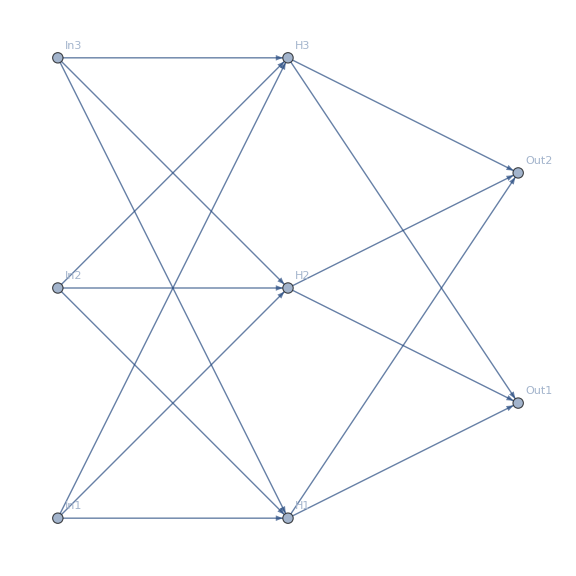
-Graphics- Null^6

```mathematica
sizes = {3,3,2};
```

Abgesehen von den Input-Neuronen des ersten Layers bekommt jedes Neuron einen Bias-Parameter b

```mathematica
b = RandomReal[{0,1},#]&/@sizes[[2;;]];
MatrixForm[#ᵀ]&/@b
```

{(0.204838
0.150673
0.88544),(0.75735
0.0999229)}

```mathematica
w = RandomReal[{0,1},{#[[1]],#[[2]]}]&/@Transpose[{sizes[[;;2]],sizes[[2;;]]}];
MatrixForm[#ᵀ]&/@w
```

{(0.899401 | 0.818488 | 0.375095
0.851423 | 0.866566 | 0.986296
0.245966 | 0.872718 | 0.652492),(0.755447 | 0.757168 | 0.99642
0.480411 | 0.96154 | 0.448348)}

```mathematica
sizes[[;;2]]
```

{3,3}

### FeedForward

Die Berechung des Netzwerks für einen Aktivierungsvektor a_in, z.B. a_in=(0.4, 0.6, 1), ist jetzt nur lineare Algebra. Von Layer a_i zu Layer a_(i+1) wird die folgende Rechnung durchgeführt:
 a_(i+1)=σ(w.a_i+b)
 Und σ ist die  sogenannte Sigmoid-Funktion, die die Aktivierung in das Intervall [0,1] abbildet

```mathematica
σ[x_]:=1/(1+ⅇ^-x)
```

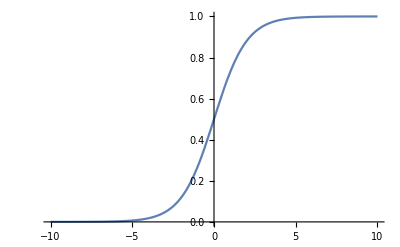

```mathematica
Plot[σ[x],{x,-10,10}]
```

```mathematica
Subscript[a, in]={0.4,-0.6,1}
```

{0.4,-0.6,1}

```mathematica
Subscript[a, 2]=σ[w[[1]]ᵀ.Subscript[a, in]+b[[1]]ᵀ]
```

{0.610306,0.722641,0.75263}

```mathematica
Subscript[a, 3]=σ[w[[2]]ᵀ.Subscript[a, 2]+b[[2]]ᵀ]
```

{0.925221,0.806185}

### Stochastic Gradient Descent

#### cost_derivative

Einfachste Kostenfunktion: Quadrate der Differenzen zwischen Label und Aktivierung, z.B.

```mathematica
Cost[a_,l_]:=1/2(a-l).(a-l)
```

```mathematica
Cost[Subscript[a, 3],{1,0}]
```

0.655526

Der Gradient der Kostenfunktion ist proportional zu (a-l)

Effektivere Kostenfunktionen sind zum Beispiel die Cross-Entropie-Funktion

#### backprop